```mathematica
(* Define points for the segment and vectors *)
p1 = {1, 1};
p2 = {4, 3};
vector2D = p2 - p1;
```

```mathematica
p3 = {1, 1, 1};
p4 = {4, 3, 5};
vector3D = p4 - p3;
```

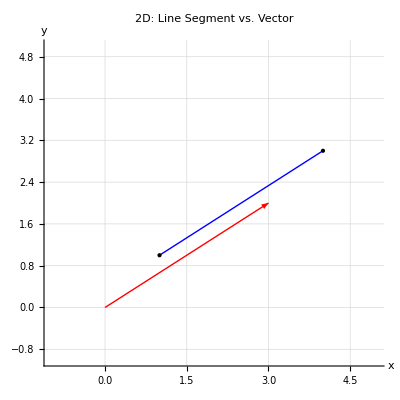

```mathematica
(* Plot for 2D case: Segment vs. Vector *)
Graphics[
 {
  {Blue, Thick, Line[{p1, p2}]}, (* Line segment from p1 to p2 *)
  {Red, Thick, Arrow[{{0, 0}, vector2D}]}, (* Vector starting at origin *)
  {Black, PointSize[Large], Point[p1]}, (* Mark segment start *)
  {Black, PointSize[Large], Point[p2]}  (* Mark segment end *)
 },
 Axes -> True, GridLines -> Automatic,
 PlotRange -> {{-1, 5}, {-1, 5}},
 AxesLabel -> {"x", "y"},
 PlotLabel -> "2D: Line Segment vs. Vector"
]
```

```mathematica
(* Plot for 3D case: Segment vs. Vector *)
Graphics3D[
 {
  {Blue, Thick, Line[{p3, p4}]}, (* Line segment from p3 to p4 *)
  {Red, Thick, Arrow[{{0, 0, 0}, vector3D}]}, (* Vector starting at origin *)
  {Black, PointSize[Large], Point[p3]}, (* Mark segment start *)
  {Black, PointSize[Large], Point[p4]}, (* Mark segment end *)
  {Green, PointSize[Large], Point[{0, 0, 0}]} (* Mark vector origin in 3D *)
 },
 Axes -> True, Boxed -> False,
 PlotRange -> {{-1, 5}, {-1, 5}, {-1, 6}},
 AxesLabel -> {"x", "y", "z"},
 PlotLabel -> "3D: Line Segment vs. Vector"
]
```

-Graphics3D-